```mathematica
$Assumtions = {L>0, β>0,η>0,Q>0,α>0,Subscript[a, 0]∈Reals,Subscript[a, 1]∈Reals};
n=300;
S[x_]:=Exp[-x^2/10]

kp[x_,ξ_]:=1/(2Sqrt[β])Exp[Sqrt[β](ξ-x)]
km[x_,ξ_]:=1/(2Sqrt[β])Exp[Sqrt[β](x-ξ)]
k[x_,ξ_]:=Piecewise[{{kp[x,ξ],x>ξ},{km[x,ξ],x<ξ}}]
kdp[x_,ξ_]=D[kp[x,ξ], x];
kdm[x_,ξ_]=D[km[x,ξ], x];
var=Rationalize[{β->3.85/0.38,η->0.2631578947368421*Q,Subscript[a, 0]->0.6,Subscript[a, 1]->0.38,α->50.58}]
```

SetDelayed::write: Tag Integer in 5000[x_,ξ_] is Protected.

$Failed

{β→385/38,η→(5 Q)/19,a_0→3/5,a_1→19/50,α→2529/50}

```mathematica
T[ξ_]:=Subscript[c, 0] kdm[0,ξ]+
η Integrate[k[x,ξ]S[x] (1-Subscript[a, 0]),{x,0,∞}]-
α Integrate[k[x,ξ],{x,0,∞}];
Subscript[T, 0][ξ_]=Piecewise[{{Expand[T[ξ]/.var],ξ>0}, {0, True}}];
```

```mathematica
Subscript[T, 1][ξ_]:=Subscript[c, 1] kp[L,ξ]+kdp[L,ξ]+Subscript[c, 2] kdm[0,ξ]+
η Integrate[k[x,ξ]S[x] (1-Subscript[a, 1]),{x,0,L},Assumptions->L>ξ>0]-
α Integrate[k[x,ξ],{x,0,L},Assumptions->L>ξ>0];
Subscript[T, 2][ξ_]:=-Subscript[c, 1]km[L,ξ]-kdm[L,ξ]+
η Integrate[k[x,ξ] S[x] (1-Subscript[a, 0]),{x,L,∞},Assumptions->ξ>L>0]-
α Integrate[k[x,ξ],{x,L,∞},Assumptions->ξ>L>0];
Subscript[F, 1][ξ_]=Piecewise[{{Expand[Subscript[T, 1][ξ]]/.var,0<ξ<L}, {0,True}}];
Subscript[F, 2][ξ_]=Piecewise[{{Expand[Subscript[T, 2][ξ]]/.var,L<ξ<∞}, {0,True}}];
```

```mathematica
Subscript[eqn, 1]=Limit[Subscript[F, 1]'[x],x->0,Direction->"FromAbove"]==0;
Subscript[eqn, 2]=Limit[Subscript[F, 1][x],x->L,Direction->"FromBelow"]==-1;
Subscript[eqn, 3]=Limit[Subscript[F, 2][x],x->L,Direction->"FromAbove"]==-1;
Subscript[eqn, 4]=Limit[Subscript[T, 0]'[x],x->0,Direction->"FromAbove"]==0;
```

```mathematica
sol=Solve[Subscript[eqn, 4]/.{Subscript[c, 0]->-1}, Q];
Subscript[Q, max]=Q/.sol[[1]]
```

(19213 √(19/(77 π)))/(125 ⅇ^(1925/76) Erfc[(5 √(77/19))/2])

```mathematica
N[(19213 √(19/(77 π)))/(125 ⅇ^(1925/76) Erfc[(5 √(77/19))/2]),20]
```

391.57182354230076862

```mathematica
tempQ={Q->Subscript[Q, max]-50};
sol=NSolve[{Subscript[eqn, 1]/.tempQ,Subscript[eqn, 2]/.tempQ,Subscript[eqn, 3]/.tempQ,-20<Subscript[c, 1]<0,-1<Subscript[c, 2]<20,0<L<10},{Subscript[c, 1],Subscript[c, 2],L},Reals]
```

{{c_1→-7.17889,c_2→4.39068,L→2.36913},{c_1→-1.64315,c_2→-0.976028,L→0.0291978}}

```mathematica
Monitor[For[Subscript[Q, 1]=IntegerPart[Subscript[Q, max]]+1;Subscript[Q, 0]=0;dQ=IntegerPart[Subscript[Q, max]]+1;ϵ=10^-15;Subscript[Q, test]=(Subscript[Q, 1]+Subscript[Q, 0])/2,dQ>ϵ,Subscript[Q, test]=(Subscript[Q, 1]+Subscript[Q, 0])/2,tempQ={Q->Subscript[Q, test]};
sol=NSolve[{Subscript[eqn, 1]/.tempQ,Subscript[eqn, 2]/.tempQ,Subscript[eqn, 3]/.tempQ,-20<Subscript[c, 1]<0,-1<Subscript[c, 2]<20,0<L<10}, {Subscript[c, 1],Subscript[c, 2],L}];
If[sol==={},dQ=Subscript[Q, test]-Subscript[Q, 0];Subscript[Q, 0]=Subscript[Q, test],dQ=Subscript[Q, 1]-Subscript[Q, test];Subscript[Q, 1]=Subscript[Q, test]];],N[dQ]]
Subscript[Q, min]=Subscript[Q, test]+dQ;
```

```mathematica
Subscript[Q, min]
```

31389452545021706387/144115188075855872

```mathematica
N[49/72057594037927936]
```

6.80012×10^-16

```mathematica
Subscript[Temps, 0]={};
Subscript[Temps, 1]={};
Monitor[For[i=0,i<n,i++,
tempQ={Q->Subscript[Q, min]+(Subscript[Q, max]-Subscript[Q, min])*i/(n-1)};
sol=NSolve[{Subscript[eqn, 1]/.tempQ,Subscript[eqn, 2]/.tempQ,Subscript[eqn, 3]/.tempQ,-20<Subscript[c, 1]<0,-1<Subscript[c, 2]<20,0<L<10}, {Subscript[c, 1],Subscript[c, 2],L}];
Subscript[Temps, 1]=Insert[Subscript[Temps, 1],{N[Q/.tempQ,5],N[Subscript[c, 2]/.sol[[1]],5]},-1];
If[Length[sol]==1,sol=Insert[sol, {Subscript[c, 2]->-1},-1],0];
Subscript[Temps, 0]=Insert[Subscript[Temps, 0],{N[Q/.tempQ,5],N[Subscript[c, 2]/.sol[[2]],5]},-1];],i]
```

```mathematica
Subscript[Temps, 2]={};
Monitor[For[i=0,i<n,i++,
tempQ={Q->i*Subscript[Q, max]/(n-1)};
sol =NSolve[Subscript[eqn, 4]/.tempQ, Subscript[c, 0]];
Subscript[Temps, 2]=Insert[Subscript[Temps, 2],{N[Q/.tempQ,5],N[Subscript[c, 0]/.sol[[1]],5]},-1];],i]
```

```mathematica
Subscript[Temps, 3]={};
Monitor[For[i=0,i<n,i++,
tempQ={Q->Subscript[Q, max]+i*Subscript[Q, max]/(n-1)};
sol=NSolve[{Subscript[eqn, 1]/.tempQ,Subscript[eqn, 2]/.tempQ,Subscript[eqn, 3]/.tempQ,-20<Subscript[c, 1]<0,-1<Subscript[c, 2]<20,0<L<10}, {Subscript[c, 1],Subscript[c, 2],L}];
Subscript[Temps, 3]=Insert[Subscript[Temps, 3],{N[Q/.tempQ,5],N[Subscript[c, 2]/.sol,5]},-1];],i]
```

```mathematica
Result=Join[Subscript[Temps, 2],Reverse[Subscript[Temps, 0]],Subscript[Temps, 1],Subscript[Temps, 3]];
Unstable=Subscript[Temps, 0];
Export["Result.txt",Result,"Table"];
Export["Result_Unstable.txt",Unstable,"Table"];
```

```mathematica
DiscretizedSolution={};
k=5000;
W=100Pi;
dx=N[Pi/W,20];
Subscript[x, val]=Table[(x-1)*dx,{x,k+1}];
```

```mathematica
tempQ={Q->340};
sol=NSolve[Subscript[eqn, 4]/.tempQ,Subscript[c, 0]];
sol=Join[tempQ,sol[[1]]];
Subscript[K, 0][x_]=Rationalize[Refine[Subscript[T, 0][x],x>0]/.sol,0];
values=Join[{N[Q]/.sol,k,dx},N[Subscript[K, 0][Subscript[x, val]]]];
Export["Ice_Only.txt",values,Format->Table];
```

```mathematica
tempQ={Q->340};
sol=NSolve[{Subscript[eqn, 1]/.tempQ,Subscript[eqn, 2]/.tempQ,Subscript[eqn, 3]/.tempQ,-20<Subscript[c, 1]<0,-1<Subscript[c, 2]<20,0<L<10}, {Subscript[c, 1],Subscript[c, 2],L}];
sol=Join[tempQ,sol[[2]]];
Subscript[K, 1][x_]=Rationalize[Refine[Subscript[F, 1][x],0<x<L]/.sol,0];
Subscript[K, 2][x_]=Rationalize[Refine[Subscript[F, 2][x],L<x]/.sol,0];
splitVal=Position[Subscript[x, val],Select[Subscript[x, val],#>L/.sol &, 1][[1]]][[1]][[1]];
Subscript[x, 1]=Subscript[x, val][[1;;splitVal-1]];
Subscript[x, 2]=Subscript[x, val][[splitVal;;]];
values=Join[{N[Q]/.sol,k,dx},N[Subscript[K, 1][Subscript[x, 1]]],N[Subscript[K, 2][Subscript[x, 2]]]];
Export["Partial_Ice_Unstable.txt",values,Format->Table];
```

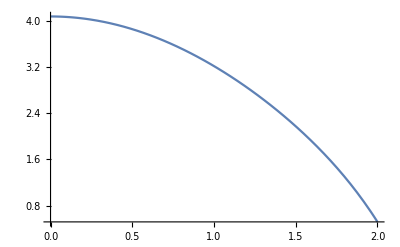

```mathematica
Plot[LOL[x],{x,-0,2},WorkingPrecision->20]
```